## Language

∀_a

Definition

S[a]⇒

∀_(x=1,…,n)P[x]==3x

∀_(x,y=1,…,n)(P[x,y]:⟺Q[x]⋁Q[y])

∀_(x,y,z=1,…^4,n)P[x]

∀_(x∈A)(P[x]:=5+x)

∀_(x,y∈A)P[x]

∀_Q[x]P[x]

∀_Q[x,y,z]P[x]

∀_(x,y,z)A[x]

■

Proof of (8)

"Show proof"

□

Proof of (7)

"Show proof"

□

```mathematica
SetSelectedNotebook[NotebookObject[{{, "Proof Navigator"}}]]
```

⁃NotebookObject⁃

```mathematica
NotebookClose[Notebooks[][[3]]]
```

```mathematica
SetOptions[Notebooks[][[2]],Visible->True]
```

```mathematica
Theorema`Common`$TMAproofObject=Theorema`Provers`Common`Private`PROOFOBJ$[{a,b,c,d}];
```

```mathematica
Attributes[NotebookPut]
```

{Protected,ReadProtected}

```mathematica
Theorema`Provers`Common`Private`$TMAproofNotebook//FullForm
```

NotebookObject[FrontEndObject[LinkObject["9tj_shm",1,1]],48]

```mathematica
Theorema`Common`$TMAproofObject
```

PROOFOBJ$[PRFINFO$[Initial,{{ID:822628176,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x,y,z)A[x],(8)},{{{ID:1346427776,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x∈A)P[x]:=5+x,(4)},{{ID:1242901413,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x=1,…,n
y=1,…,n)IffDef[P[x,y],Q[x]||Q[y]],(10)},{{ID:1636935908,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x=1,…,n)P[x]=3 x,(1)}}],PROOFSIT$[{{ID:822628176,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x,y,z)A[x],(8)},{{{ID:1346427776,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x∈A)P[x]:=5+x,(4)},{{ID:1242901413,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x=1,…,n
y=1,…,n)IffDef[P[x,y],Q[x]||Q[y]],(10)},{{ID:1636935908,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x=1,…,n)P[x]=3 x,(1)}},{},pending,InferenceRules→inferenceRules[prover1]]]

```mathematica
Hyperlink[xxx,{CurrentValue[Theorema`Provers`Common`Private`$TMAproofNotebook,"NotebookFileName"],"ID:1874491785"}]
```

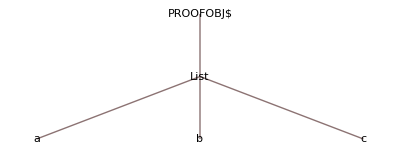

```mathematica
Theorema`Common`showProofNavigation[Theorema`Provers`Common`Private`$TMAproofObject]
```

```mathematica
Theorema`Common`displayProof[Theorema`Common`$TMAproofObject]
```

```mathematica
f=Theorema`Common`$tmaEnv[[1,2]]
```

∀_a S[a]⇒∀_(x=1,…,n)P[x]=3 x

```mathematica
Theorema`Common`freeVariables[f]
```

{}

```mathematica
ToString[{"ID:1","Source:/home"},InputForm]//FullForm
```

"{"ID:1", "Source:/home"}"

```mathematica
ToExpression[%]//FullForm
```

List["ID:1","Source:/home"]

```mathematica
Theorema`Common`transferToComputation[f,{"ID:1","Source:/home"}]
```

```mathematica
Clear[Theorema`Computation`Knowledge`P$TM]
```

```mathematica
??Theorema`Computation`Knowledge`P$TM
```

Theorema`Computation`Knowledge`P$TM

P[x_]/;activeComputationKB[{ID:1636935908,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb}]&&S[a]&&(isInteger[x]&&1≤x&&x≤n):=3 x
 
P[x_,y_]/;activeComputationKB[{ID:1242901413,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb}]&&S[a]&&(isInteger[x]&&1≤x&&x≤n)&&(isInteger[y]&&1≤y&&y≤n):=Q[x]||Q[y]
 
P[x_]/;activeComputationKB[{ID:1346427776,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb}]&&S[a]&&x∈A:=5+x

P[3]

P[3]

P[3]

9

```mathematica
Theorema`Common`$tmaEnv
```

{{{ID:822628176,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(x,y,z)A[x],(8)},{{ID:1491028062,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(Q[x]
Q[y]
Q[z])P[x],(7)},{{ID:1874491785,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_Q[x]P[x],(6)},{{ID:1421485859,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(x∈A
y∈A)P[x],(5)},{{ID:1346427776,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(x∈A)P[x],(4)},{{ID:330716980,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(x=1,…^4,n
y=1,…^4,n
z=1,…^4,n)P[x],(3)},{{ID:1242901413,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a∀_(x=1,…,n
y=1,…,n)P[x],(2)},{{ID:1636935908,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb},∀_a S[a]⇒∀_(x=1,…,n)P[x],(1)}}

```mathematica
Theorema`Common`$tmaEnv//InputForm
```

{{{"ID:822628176", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`SIMPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM]], 
      Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
        Theorema`Knowledge`y$TM]], Theorema`Language`SIMPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`z$TM]]], True, 
     Theorema`Knowledge`A$TM[Theorema`Language`VAR$[
       Theorema`Knowledge`x$TM]]]]], "(8)"}, 
 {{"ID:1491028062", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`PREDRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 
       Theorema`Knowledge`Q$TM], Theorema`Language`PREDRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`y$TM], 
       Theorema`Knowledge`Q$TM], Theorema`Language`PREDRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`z$TM], 
       Theorema`Knowledge`Q$TM]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(7)"}, 
 {{"ID:1874491785", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`PREDRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 
       Theorema`Knowledge`Q$TM]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(6)"}, 
 {{"ID:1421485859", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`SETRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 
       Theorema`Knowledge`A$TM], Theorema`Language`SETRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`y$TM], 
       Theorema`Knowledge`A$TM]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(5)"}, 
 {{"ID:1346427776", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`SETRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 
       Theorema`Knowledge`A$TM]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(4)"}, 
 {{"ID:330716980", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`STEPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 1, 
       Theorema`Knowledge`n$TM, 4], Theorema`Language`STEPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`y$TM], 1, 
       Theorema`Knowledge`n$TM, 4], Theorema`Language`STEPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`z$TM], 1, 
       Theorema`Knowledge`n$TM, 4]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(3)"}, 
 {{"ID:1242901413", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Implies$TM[
    Theorema`Knowledge`S$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]], Theorema`Language`Forall$TM[
     Theorema`Language`RNG$[Theorema`Language`STEPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 1, 
       Theorema`Knowledge`n$TM, 1], Theorema`Language`STEPRNG$[
       Theorema`Language`VAR$[Theorema`Knowledge`y$TM], 1, 
       Theorema`Knowledge`n$TM, 1]], True, Theorema`Knowledge`P$TM[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]]], "(2)"}, 
 {{"ID:1636935908", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`a$TM]]], True, Theorema`Language`Forall$TM[
    Theorema`Language`RNG$[Theorema`Language`STEPRNG$[
      Theorema`Language`VAR$[Theorema`Knowledge`x$TM], 1, 
      Theorema`Knowledge`n$TM, 1]], True, Theorema`Knowledge`P$TM[
     Theorema`Language`VAR$[Theorema`Knowledge`x$TM]]]], "(1)"}}

Definition

∀_x

f[x]:=Program[
Module[{y=x,a},Do[y=y∪{i},{i,2,5}];y]]

■

```mathematica
Theorema`Common`$tmaEnv//InputForm
```

{{{"ID:412145113", 
   "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}, 
  Theorema`Language`Forall$TM[Theorema`Language`RNG$[
    Theorema`Language`SIMPRNG$[Theorema`Language`VAR$[
      Theorema`Knowledge`x$TM]]], True, Theorema`Language`EqualDef$TM[
    Theorema`Knowledge`f$TM[Theorema`Language`VAR$[
      Theorema`Knowledge`x$TM]], Theorema`Language`Module$TM[
     Theorema`Language`List$TM[Theorema`Language`Assign$TM[
       Theorema`Knowledge`y$TM, Theorema`Language`VAR$[
        Theorema`Knowledge`x$TM]], Theorema`Knowledge`a$TM], 
     Theorema`Language`CompoundExpression$TM[Theorema`Language`Do$TM[
       Theorema`Language`Assign$TM[Theorema`Knowledge`y$TM, 
        Theorema`Language`Union$TM[Theorema`Knowledge`y$TM, 
         Theorema`Language`List$TM[Theorema`Knowledge`i$TM]]], 
       Theorema`Language`List$TM[Theorema`Knowledge`i$TM, 2, 5]], 
      Theorema`Knowledge`y$TM]]]], "(9)"}}

```mathematica
??Theorema`Computation`Knowledge`f$TM
```

Theorema`Computation`Knowledge`f$TM

f[x_]/;activeComputationKB[{ID:412145113,Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb}]:=Module[{y=x,a},Do[y=y∪{i},{i,2,5}];y]

```mathematica
InputForm[DownValues[Theorema`Computation`Knowledge`f$TM]]
```

{HoldPattern[Theorema`Computation`Knowledge`f$TM[
     Theorema`Computation`Knowledge`x$TM_] /; 
    Theorema`Computation`Language`Private`activeComputationKB[
     {"ID:412145113", 
      "Source:/home/wwindste/Theorema.2/Theorema/Test/Language.nb"}]] :> 
  Theorema`Computation`Language`Module$TM[
   Theorema`Computation`Language`List$TM[
    Theorema`Computation`Knowledge`y$TM = 
     Theorema`Computation`Knowledge`x$TM, 
    Theorema`Computation`Knowledge`a$TM], 
   Theorema`Computation`Language`Do$TM[
     Theorema`Computation`Knowledge`y$TM = 
      Theorema`Computation`Language`Union$TM[
       Theorema`Computation`Knowledge`y$TM, 
       Theorema`Computation`Language`List$TM[
        Theorema`Computation`Knowledge`i$TM]], 
     Theorema`Computation`Language`List$TM[
      Theorema`Computation`Knowledge`i$TM, 2, 5]]; 
    Theorema`Computation`Knowledge`y$TM]}

f[{3}]

f[{3}]

f[{3}]

((({3}∪{2})∪{3})∪{4})∪{5}

f[{3}]

Module[{y={3},a},Do[y=y∪{i},{i,2,5}];y]

f[{3}]

{3}

```mathematica
InputForm[%]
```

Theorema`Computation`Language`Set$TM[3]

## Computation

∀_(x=1,…,n)P[x]

∀_(x=1,…,n)P[x]

∀_(x=1,…,n)P[x]

∀_(x=1,…,n)P[x]

∀_(x=1,…,7+3)P[x]

P[1]&&P[2]&&P[3]&&P[4]&&P[5]&&P[6]&&P[7]&&P[8]&&P[9]&&P[10]

∀_(x=1,…,7+3)P[x]

∀_(x=1,…,7+3)P[x]

∀_(x=1,…^2,7+3)P[x]

P[1]&&P[3]&&P[5]&&P[7]&&P[9]

∃_(x=1,…,3)P[x]

P[1]||P[2]||P[3]

∃_(x=1,…,n)P[x]

∃_(x=1,…,n)P[x]

∃_(x=1,…,7+3)P[x]

P[1]||P[2]||P[3]||P[4]||P[5]||P[6]||P[7]||P[8]||P[9]||P[10]

∃_(x=1,…,7+3)P[x]

∃_(x=1,…,7+3)P[x]

1+1

1+1

1+1

2

∃_(x=1,…^3,7+3)P[x]

P[1]||P[4]||P[7]||P[10]

∀_(a∈{1,2})(∀_(x,y,z))_(x>a∧P[x,y,z])Q[a,x,y,z]

(∀_x)_(x>1)(∀_(y,z))_P[x,y,z]Q[1,x,y,z]&&(∀_x)_(x>2)(∀_(y,z))_P[x,y,z]Q[2,x,y,z]

∀_(x∈{1,2})False

False

∀_(x∈{})P[x]

True

∀_(x∈{})False

True

(∀_(x∈{1,2,3,5}))_(x<2)P[x]

P[1]

(∀_(x∈{1,2,3,5}))_(2|x)P[x]

((2|1)⇒P[1])&&((2|2)⇒P[2])&&((2|3)⇒P[3])&&((2|5)⇒P[5])

(∀_(x∈{1,2,3,5}))_(2|x)False

!(2|1)&&!(2|2)&&!(2|3)&&!(2|5)

∀_(x∈{1,2,3,5})(∃_(y=1,…,x))_(y≥x)y≤x

True

∀_(x∈{1,2,3,5})(∃_(y=1,…,x))_(y≥x)y<x

False

∀_(x∈{1,2,3,5})(∃_(y=1,…,x-1))_(y≥x)P[x,y]

False

∀_(x∈{1,2,3,5})(∃_(y=1,…,x))_(y≥x)P[x,y]

P[1,1]&&P[2,2]&&P[3,3]&&P[5,5]

∀_(x∈{1,2,3,5})(∃_(y=1,…,x+1))_(y≥x)P[x,y]

(P[1,1]||P[1,2])&&(P[2,2]||P[2,3])&&(P[3,3]||P[3,4])&&(P[5,5]||P[5,6])

∀_(x∈{1,2,3,5})∃_(y=1,…,x+1)P[x,y]

(P[1,1]||P[1,2])&&(P[2,1]||P[2,2]||P[2,3])&&(P[3,1]||P[3,2]||P[3,3]||P[3,4])&&(P[5,1]||P[5,2]||P[5,3]||P[5,4]||P[5,5]||P[5,6])

∀_(x∈{1,2,3,5})∃_(y=1,…,x+1)P[x,y]

∀_(x∈{1,2,3,5})∃_(y=1,…,x+1)P[x,y]

```mathematica
InputForm[%]
```

Theorema`Computation`Language`Forall$TM[Theorema`Computation`Language`RNG$[
  Theorema`Computation`Language`SETRNG$[Theorema`Computation`Language`VAR$[
    Theorema`Computation`Knowledge`x$TM], 
   Theorema`Computation`Language`Set$TM[1, 2, 3, 5]]], True, 
 Theorema`Computation`Language`Exists$TM[
  Theorema`Computation`Language`RNG$[
   Theorema`Computation`Language`STEPRNG$[
    Theorema`Computation`Language`VAR$[
     Theorema`Computation`Knowledge`y$TM], 1, 
    Theorema`Computation`Language`Plus$TM[
     Theorema`Computation`Language`VAR$[
      Theorema`Computation`Knowledge`x$TM], 1], 1]], True, 
  Theorema`Computation`Knowledge`P$TM[Theorema`Computation`Language`VAR$[
    Theorema`Computation`Knowledge`x$TM], 
   Theorema`Computation`Language`VAR$[
    Theorema`Computation`Knowledge`y$TM]]]]